```mathematica
σ = .5;
fD = 10.;
fM = 1.0;
```

```mathematica
a = fM^2/σ^2;
b=fM fD/σ^2;
c = fD^2/σ^2;
σc=.2;
μ=1.;
```

## Beginning

```mathematica
Log[10.]
```

2.30259

```mathematica
FDist = LogNormalDistribution[Log[10.],0.2]
```

LogNormalDistribution[2.30259,0.2]

```mathematica
fDs = RandomVariate[FDist,50];
```

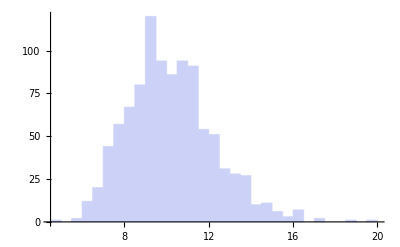

```mathematica
Histogram[RandomVariate[FDist,1000]]
```

```mathematica
Plot3D[pJ2[F,c0],{F,5,40},{c0,0.01,3},PlotRange->{Full,Full,{0,1}},PlotPoints->{100,100}]
```

-Graphics3D-

```mathematica
σ = .2
μ = σ^2
```

0.2

0.04

```mathematica
pc[c0_]:=1/(√(2 π)σ c0)Exp[(-(Log[c0] -μ)^2)/(2 σ^2)](*mode equal to 1*)
pc2[c0_]:=1/(√(2 π)σ c0)Exp[(-Log[c0]^2)/(2 σ^2)](*mean equal to 1*)
pc3[c0_]:=1/(√(2 π)σ c0)Exp[(-(Log[c0] -1)^2)/(2 σ^2)]
```

```mathematica
NIntegrate[pc[c0], {c0,0,1}]
NIntegrate[ pc[c0], {c0,1,∞}]
NIntegrate[ pc[c0],{c0,0,∞}]
```

0.158655

0.841345

1.

```mathematica
pc2[1]
```

1.99471

```mathematica
pc2[0.1]
```

3.29281×10^-28

```mathematica
pc2[10]
```

3.29281×10^-30

```mathematica
NIntegrate[pc2[c0], {c0,0.1,1}]
NIntegrate[ pc2[c0], {c0,1,10}]
NIntegrate[ pc2[c0],{c0,0,∞}]
```

0.489349

0.489349

1.

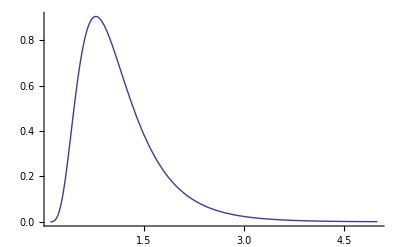

```mathematica
Plot[pc2[c],{c,0.1,5}]
```

```mathematica
FindMaximum[pc[c0],{c0,1}]
FindMaximum[pc2[c0],{c0,1}]
FindMaximum[pc3[c0],{c0,1}]
```

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{1.95521,{c0→1.}}

{2.03501,{c0→0.960789}}

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{1.99471,{c0→1.}}

```mathematica
func0[F_,c0_]:=Exp[-0.5 * (c0^2 F^2 a-2 b F c0 +c)]
func[F_,c0_]:=func0[F,c0] pc[c0]
func2[F_,c0_]:=func0[F,c0]pc2[c0]
func3[F_,c0_]:=func0[F,c0]pc3[c0]
```

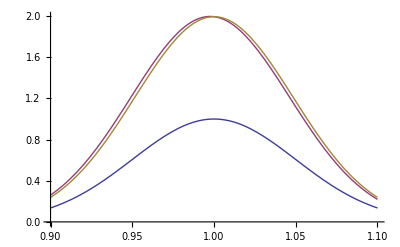

```mathematica
Plot[{func0[10,c0],func2[10,c0],func3[10,c0]},{c0,0.9,1.1}]
```

```mathematica
FindMaximum[func[10,c0],{c0,1}]
FindMaximum[func2[10,c0],{c0,1}]
FindMaximum[func3[10,c0],{c0,1}]
```

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{1.95521,{c0→1.}}

{1.99706,{c0→0.997642}}

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{1.99471,{c0→1.}}

```mathematica
pF[F_]:=NIntegrate[ func[F,c0],{c0,0,∞}]
pF2[F_]:=NIntegrate[ func2[F,c0],{c0,0,∞}]
pF3[F_]:=NIntegrate[ func3[F,c0],{c0,0,∞}]
```

```mathematica
FindMaximum[pF[F],{F,10.}]
FindMaximum[pF2[F],{F,10.}]
FindMaximum[pF3[F],{F,10.}]
```

NIntegrate::inumr: The integrand 1.99471\ ⅇ^-0.5\ (400.  - 80.\ c0\ F + 4.\ c0^2\ F^2) - 12.5\ (-0.04 + Log[c0])^2/c0
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in c0 near {c0} = {1.08986}. NIntegrate obtained 2.0017×10^-10 and 3.94822×10^-15 for the integral and error estimates.

{0.243052,{F→9.57382}}

NIntegrate::inumr: The integrand 1.99471\ ⅇ^-0.5\ (400.  - 80.\ c0\ F + 4.\ c0^2\ F^2) - 12.5\ Log[c0]^2/c0
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in c0 near {c0} = {0.954258}. NIntegrate obtained -6.69298×10^-13 and 3.91522×10^-15 for the integral and error estimates.

{0.243052,{F→9.96454}}

NIntegrate::inumr: The integrand 1.99471\ ⅇ^-12.5\ (-1 + c0)^2 - 0.5\ (400.  - 80.\ c0\ F + 4.\ c0^2\ F^2)
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in c0 near {c0} = {1.08986}. NIntegrate obtained 2.34918×10^-9 and 3.00025×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in c0 near {c0} = {1.00791}. NIntegrate obtained -2.39912×10^-14 and 3.08596×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in c0 near {c0} = {1.07294}. NIntegrate obtained 2.34173×10^-9 and 3.37321×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.24697,{F→9.62831}}

```mathematica
NIntegrate[NIntegrate[F func2[F,c0],{c0,0,∞}],{F,0,∞}]
```

NIntegrate::inumr: The integrand 1.99471\ ⅇ^-0.5\ (400.  - 80.\ c0\ F + 4.\ c0^2\ F^2) - 12.5\ Log[c0]^2\ F/c0
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

13.577

```mathematica
$Assumptions = {{a1,a2,a3,a4,a5} ∈ Reals, a1 > 0}
```

{(a1|a2|a3|a4|a5)∈Reals,a1>0}

## Starting again

```mathematica
pJ[F_,c0_,fD_,fM_,σ_,σc_]:=1/(2 π σ σc c0)Exp[-(fD - F c0 fM)^2/(2 σ^2)]Exp[(-Log[c0]^2)/(2 σc^2)]
```

```mathematica
FindMaximum[pJ[F,c0, 10, 1 , 0.5, 0.2],{{F,10},{c0,1}}]
FindMaximum[pJ[F,c0, 10, 1 , 0.5, 0.2],{{F,10},{c0,0.8}}]
FindMaximum[pJ[F,c0, 10, 1 , 0.5, 0.2],{{F,10},{c0,1.2}}]
```

FindMaximum::nrnum: The function value -2.41136187049399×10^-2151 - 1.6086302902787×10^-2151\ ⅈ is not a real number at {F, c0} = {10., -4.02494}.

{1.59155,{F→10.,c0→1.}}

{1.6237,{F→10.4081,c0→0.960789}}

FindMaximum::nrnum: The function value -1.70985336989036×10^-8037 + 5.84610920236096×10^-8038\ ⅈ is not a real number at {F, c0} = {10.3226, -8.36616}.

{1.58993,{F→9.97729,c0→0.999806}}

```mathematica
pJ[10,0.9, 10, 1, 0.5, 0.2]
```

0.208317

```mathematica
Plot3D[pJ[F,c0, 10, 1, 0.5, 0.1],{F,9.9,10.5},{c0,0.93,1.01},PlotRange->{Full,Full,{0,4}},PlotPoints->{100,100}]
```

-Graphics3D-

## Approximating Integrals

```mathematica
func[x_]:=1/x^4 Exp[-a x^2+b x - c Log[x]^2]
```

```mathematica
Series[Log[x]^2,{x,1,7}]
```

(x-1)^2-(x-1)^3+11/12 (x-1)^4-5/6 (x-1)^5+137/180 (x-1)^6-7/10 (x-1)^7+O[x-1]^8

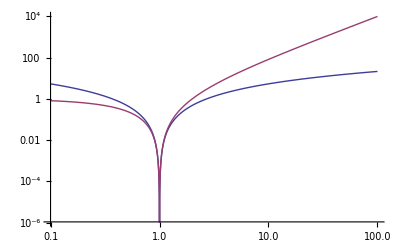

```mathematica
LogLogPlot[{Log[x]^2,(x-1)^2},{x,0.1,100}]
```

```mathematica
pJ[F_,c0_,fD_,fM_,σ_,σc_]:=1/(2 π σ σc c0)Exp[-0.5 ((F^2 c0^2 fM^2)/σ^2- (2 F c0 fM fD)/σ^2+Log[c0]^2/σc^2+fD^2/σ^2)]
```

```mathematica
pJApprox[F_,c0_,fD_,fM_,σ_,σc_]:=1/(2 π σ σc)Exp[-0.5 ((F^2 c0^2 fM^2)/σ^2- (2 F c0 fM fD)/σ^2+(c0-1)^2/σc^2+fD^2/σ^2)](*This is approximating the prior as a Gaussian *)
```

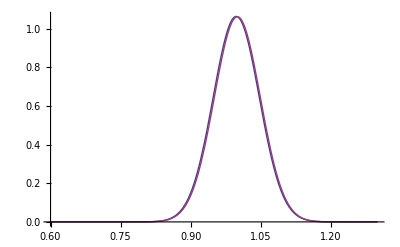

```mathematica
Plot[{pJ[10,c0, 10, 1 , 0.5, 0.3],pJApprox[10,c0, 10, 1 , 0.5, 0.3]},{c0,0.6,1.3}]
```

```mathematica
NIntegrate[pJ[10,c0, 10, 1 , 0.5, 0.3],{c0,0,∞}]
```

0.131468

```mathematica
NIntegrate[pJApprox[10,c0, 10, 1 , 0.5, 0.3],{c0,0,∞}]
```

0.131171

Keeping only the 2nd order term is also fine. But you definitely want to keep an even number of terms, otherwise the integral diverges as you go to ∞. Turns out, keeping the 2nd order term and dropping the front prefactor constant actuall makes the posterior look pretty Gaussian.

## Priors on the c1

```mathematica
σc0 = 0.5;
σc1 = 0.1;
```

```mathematica
pc0[c0_]:=1/(√(2 π)σc0 c0)Exp[(-Log[c0]^2)/(2 σc0^2)]
```

```mathematica
pc1[c1_]:=1/(√(2 π)σc1)Exp[-c1^2/(2 σc1^2)]
```

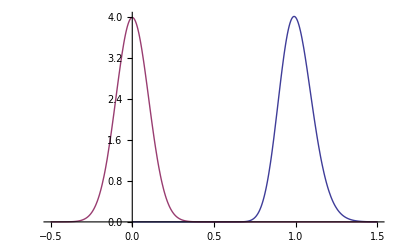

```mathematica
Plot[{pc0[c],pc1[c]},{c,-0.5,1.5}]
```

```mathematica
Plot3D[pc0[c0]pc1[c1],{c0,0.1,1.7},{c1,-0.3,0.3},PlotRange->{Full,Full,{0,4}},PlotPoints->{100,100}]
```

-Graphics3D-

### Lognormal approximation

## Chebyshev Coefficients

```mathematica
NIntegrate[func[10,c0],{c0,0,∞}]
```

0.12183

Which way should we be scaling these higher order Chebyshev coefficients?

```mathematica
1/1.2
```

0.833333

```mathematica
f[x_]:=100.
k[x_,c0_,c1_,c2_,c3_]:=c0 ChebyshevT[0,x](1 + c1 ChebyshevT[1,x] + c2 ChebyshevT[2,x] +c3 ChebyshevT[3,x] )
k2[x_,c0_,c1_,c2_,c3_]:=c0 ChebyshevT[0,x] + c1 ChebyshevT[1,x] + c2 ChebyshevT[2,x] +c3 ChebyshevT[3,x]
```

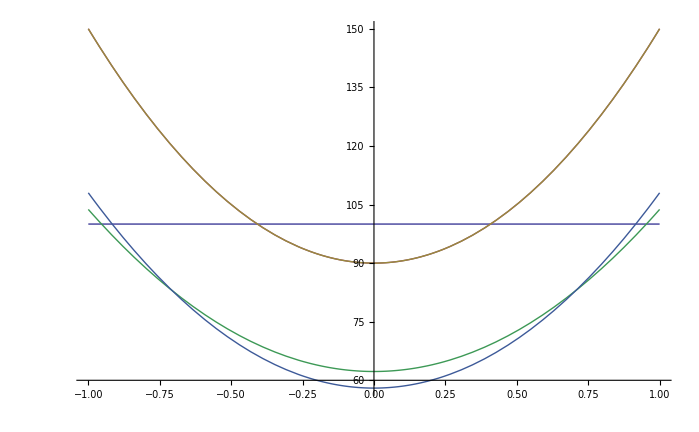

```mathematica
Plot[{f[x],f[x]k[x,1.2,0,.25,0],f[x]k2[x,1.2,0,0.30,0],f[x]k[x,0.83,0,0.25,0],f[x]k2[x,0.83,0,0.25,0]},{x,-1,1}]
```